```mathematica
(* let there be a parabolic mirror(concave)defined by x^2=4ay
let a=1 for plots*)
```

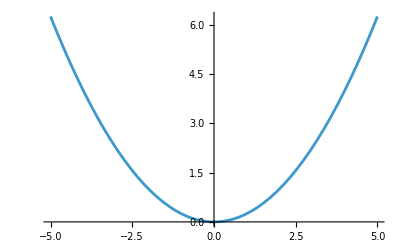

```mathematica
Plot[x^2/4,{x,-5,5}]
```

```mathematica
(* by definition center of curvature is point of intersection of Principal axis(here y=0) and Normal at the point on mirror
let x=t_> y=t^2/4a
dy/dx=2x/4a=x/2a
dy/dx shall give slope at the point 
hence the normal shall be given by -2a/x=-2a/t

(y-t^2/4a)=-2a(x-t)/t
it intersects with principal axis.
to find coordinates of CoC->x=0
in RHS -2a(-t)/t=2a
hence
y=t^2/(4a)+2a
*)
```

#### Note; in spherical concave mirror R=2a. hence if distance from principal axis(x=t) is small then it works like spherical but for higher distances it gets further and further away. Hence, it is not fixed. It enables the i for larger distances<90. In spherical, as it rounds up faster, distance CQ(c is center of curvature, Q is point at which light is incident) increases rapidly and thus, i->90 and r->90, thus it goes without reflection, but in case of parabolic, it is slow. thus more of the light is reflected towards, foci-> more converging ability.

```mathematica
Manipulate[Plot[{x^2/4,t^2/4+2},{x,-5,5}],{t,-5,5}]
```

```mathematica
(* the intersection of orange line and y axis is center of curvature for particular t(=x)*)
```

```mathematica
(* also t^2/4a is distance from y axis. hence y axis+ center of curvature of sphere as shown below*)
```

```mathematica
Manipulate[Plot[{x^2/4,t+2},{x,-5,5}],{t,0,4}]
```